```mathematica
cycA=Cycles[{{2,3},{4,5}}];
cycB=Cycles[{{1,2,3,4,5}}];
cycC=Cycles[{{3,4,5}}];
cycB2=PermutationPower[cycB,2];
```

```mathematica
groupA5 =PermutationGroup[{cycA,cycB}];
```

```mathematica
setC2=GroupOrbits[groupA5 ,{cycA}][[1]];
setC3=GroupOrbits[groupA5 ,{cycC}][[1]];
setC4=GroupOrbits[groupA5 ,{cycB}][[1]];
setC5 =GroupOrbits[groupA5 ,{cycB2}][[1]];
setZ5=Range[5];
```

```mathematica
setI=Tuples[{setC4,setZ5}];
```

```mathematica
ClearAll[funS,funD];
funS[cycle_,k_,i_]:={cycle,PermutationReplace[k,PermutationPower[cycle,i]]};

funD[cycle_,k_]:=Module[{gamma},
(*gamma[n_]:=Nest[PermutationReplace[#,cycle]&,k,n];*)
gamma[n_]:=PermutationReplace[k,PermutationPower[cycle,n]];
{Cycles[{{k,gamma[2],gamma[1],gamma[4],gamma[3]}}],k}
];
```

```mathematica
setS = {#,funS[#1,#2,1]&@@#}&/@setI;
setIS = {#,funS[#1,#2,-1]&@@#}&/@setI;
setD = ({#,funD[#1,#2]&@@#}&/@setI)//DeleteDuplicates[#,(Reverse@#2==#1&)]&;
setW = Subsets[setI,{2}];
groupToIdx=AssociationThread[setS[[All,1]],Range@60];
```

```mathematica
idxS=setS/.groupToIdx;
idxIS=setIS/.groupToIdx;
idxD=setD/.groupToIdx;
idxW=setW/.groupToIdx;idxA=Flatten[Table[{{i,j},funS[i,j,1],funS[i,j,-1],funD[i,j]},{i,setC4},{j,setZ5}],1]/.groupToIdx;
```

```mathematica
ClearAll[q,p,qI,pI,qD,pD,qDD,pDD];
q=Map[Symbol,Table[{"qx"<>i,"qy"<>i,"qz"<>i},{i,ToString/@Range[60]}],{2}];
p=Map[Symbol,Table[{"px"<>i,"py"<>i,"pz"<>i},{i,ToString/@Range[60]}],{2}];
pars={a,b1,b2,b3,l1,l2,l3};
qI=Map[Symbol,Table[{"qIx"<>i,"qIy"<>i,"qIz"<>i},{i,ToString/@Range[60]}],{2}];
pI=Map[Symbol,Table[{"pIx"<>i,"pIy"<>i,"pIz"<>i},{i,ToString/@Range[60]}],{2}];
parsI={aI,bI1,bI2,bI3,lI1,lI2,lI3};
qD=Map[Symbol,Table[{"qDx"<>i,"qDy"<>i,"qDz"<>i},{i,ToString/@Range[60]}],{2}];
pD=Map[Symbol,Table[{"pDx"<>i,"pDy"<>i,"pDz"<>i},{i,ToString/@Range[60]}],{2}];
parsD={aD,bD1,bD2,bD3,lD1,lD2,lD3};
qDD=Map[Symbol,Table[{"qDDx"<>i,"qDDy"<>i,"qDDz"<>i},{i,ToString/@Range[60]}],{2}];
pDD=Map[Symbol,Table[{"pDDx"<>i,"pDDy"<>i,"pDDz"<>i},{i,ToString/@Range[60]}],{2}];
parsDD={aDD,bDD1,bDD2,bDD3,lDD1,lDD2,lDD3};
ClearAll[x,xI,xD,xDD];
x=Flatten@{q,p};
xI=Flatten@{qI,pI};
xD=Flatten@{qD,pD};
xDD=Flatten@{qDD,pDD};
ClearAll[mI,mJ];
mI=IdentityMatrix[360];
mJ=ArrayFlatten[{{0,IdentityMatrix[180]},{-IdentityMatrix[180],0}}];
```

```mathematica
ClearAll[potU]
potU[q_]:=(Total[{
E0((1-Exp[-beta(√((#1-#2).(#1-#2))-r0)])^2-1)&@@@Map[Part[q,#]&,idxS,{2}],E0((1-Exp[-beta(√((#1-#2).(#1-#2))-r0)])^2-1)&@@@Map[Part[q,#]&,idxD,{2}](*,
eps(-2 sig^6 ((#1-#2).(#1-#2))^-3+sig^12((#1-#2).(#1-#2))^-6)&@@@Map[q[#]&,setW,{2}]*)
},2]+Total[1/2 k0(((#1-#2)/(√((#1-#2).(#1-#2)))).((#1-#3)/(√((#1-#3).(#1-#3))))+1/2)^2+1/2 k0(((#1-#4)/(√((#1-#4).(#1-#4)))).((#1-#2)/(√((#1-#2).(#1-#2))))+1/2)^2+1/2 k0(((#1-#4)/(√((#1-#4).(#1-#4)))).((#1-#3)/(√((#1-#3).(#1-#3))))+1/2)^2&@@@Map[Part[q,#]&,idxA,{2}]]+
kp Total[MapThread[(1-(#1.#2)^2)+(1-(#1.#3)^2)+(1-(#1.#4)^2)&,{Cross[(#4-#2)/(√((#4-#2).(#4-#2))),(#4-#3)/(√((#4-#3).(#4-#3)))]&@@@Map[Part[q,#]&,idxA,{2}],Cross[(#1-#2)/(√((#1-#2).(#1-#2))),(#1-#3)/(√((#1-#3).(#1-#3)))]&@@@Map[Part[q,#]&,idxA,{2}],Cross[(#1-#4)/(√((#1-#4).(#1-#4))),(#1-#3)/(√((#1-#3).(#1-#3)))]&@@@Map[Part[q,#]&,idxA,{2}],Cross[(#1-#4)/(√((#1-#4).(#1-#4))),(#1-#2)/(√((#1-#2).(#1-#2)))]&@@@Map[Part[q,#]&,idxA,{2}]}](*]*)])/.{E0->6.1322`30,beta->1.8502`30,r0->1.4322`30,eps->0.0115`30,(*sig->3.4681`30*)sig->1`30,k0->10`30,kp->0.346`30};
```

```mathematica
ClearAll[H]
H[q_,p_]:=(Total[p^2/2,2]+potU[q]);
```

```mathematica
ClearAll[P,L]
(* Linear momentum *)
P[p_]:=Total@p;
(* Angular momentum *)
L[q_,p_]:=Total@MapThread[Cross[#1,#2]&,{q,p}];
```

```mathematica
ClearAll[numH,numP,numL];
numH=Experimental`CreateNumericalFunction[Flatten@{qD,pD},{H[qD,pD]},{1}];
numP=Experimental`CreateNumericalFunction[Flatten@{qD,pD},P[pD],{3}];
numL=Experimental`CreateNumericalFunction[Flatten@{qD,pD},L[qD,pD],{3}];
```

```mathematica
ClearAll[numGH,numGP,numGL];
numGH[z_?(VectorQ[#,NumericQ]&)]:=numH["Gradient"[z]][[1]];
numGP[z_?(VectorQ[#,NumericQ]&)]:=numP["Gradient"[z]];
numGL[z_?(VectorQ[#,NumericQ]&)]:=numL["Gradient"[z]];
```

```mathematica
ClearAll[rhsDE];
rhsDE[z_?(VectorQ[#,NumericQ]&),par_?(VectorQ[#,NumericQ]&),T_?NumericQ]:=(T mJ+par[[1]] mI).numGH[z]+par[[2;;4]].numGP[z]+par[[5;;7]].numGL[z]
```

```mathematica
(* uMin está ordenada con respecto a setI *)
uMin=Import[NotebookDirectory[]<>"FullEquilibrium.m"];
eigenS=Import[NotebookDirectory[]<>"eigenSystem.m"];
```

```mathematica
(* Definition of the extended system, its jacobian and the flux *)
Clear[fWrap,f,eJacF,fluxWrap,flux]
(* Wrapper for the extended system *)
fWrap=Quiet@ParametricNDSolveValue[{y'[t]==rhsDE[y[t],parsD,TD],y[0]==xD},
{
y[1]-y[0],
(xD-xDD).mJ.numGH[xDD],
Table[(xD-xDD).mJ.(numGP[xDD][[i]]),{i,3}],
Table[(xD-xDD).mJ.(numGL[xDD][[i]]),{i,3}]
},{t,0,1},Flatten@{xD,parsD,TD,xDD},Method->"ExplicitRungeKutta"];
(* Extended system *)
f[x_?(VectorQ[#,NumericQ]&),pars_?(VectorQ[#,NumericQ]&),T_?NumericQ,xP_?(VectorQ[#,NumericQ]&)]:=Flatten[Evaluate[fWrap]@@Flatten@{x,pars,T,xP},1];
(* Extended jacobian (w.r. to x, pars and t *)
eJacF[x_?(VectorQ[#,NumericQ]&),pars_?(VectorQ[#,NumericQ]&),T_?NumericQ,xP_?(VectorQ[#,NumericQ]&)]:=Experimental`CreateNumericalFunction[Flatten@{xD,parsD,TD},
f[xD,parsD,TD,xP],{367},Jacobian->"FiniteDifference"]["Jacobian"[Flatten@{x,pars,T}]];
fJac[x_?(VectorQ[#,NumericQ]&),pars_?(VectorQ[#,NumericQ]&),T_?NumericQ,xP_?(VectorQ[#,NumericQ]&)]:=Experimental`CreateNumericalFunction[Flatten@{xD,parsD},
f[xD,parsD,T,xP],{367},Jacobian->"FiniteDifference"]["Jacobian"[Flatten@{x,pars}]];
(* Flux wrapper *)
fluxWrap=ParametricNDSolveValue[{y'[t]==rhsDE[y[t],parsD,TD],y[0]==xD},y,{t,0,1},Flatten@{xD,parsD,TD},Method->"ExplicitRungeKutta"];
(* Flux *)
flux[x_?(VectorQ[#,NumericQ]&),pars_?(VectorQ[#,NumericQ]&),T_?NumericQ]:=Evaluate[fluxWrap]@@Flatten@{x,pars,T};
```

```mathematica
DeleteDuplicates[{Count[N[Chop@eigenS[[1]],16],#],#}&/@N[Chop@eigenS[[1]],16]]//Row[{TableForm[#[[;;24]],TableHeadings->{Automatic,{"Mult.","Value"}}],"\t\t",TableForm[Join[#[[25;;]],{{"",""}}],TableHeadings->{Range[25,47],{"Mult.","Value"}}]}]&
```

| Mult. | Value
1 | 5 | 176.5356153216033
2 | 5 | 176.3661144387365
3 | 4 | 164.083342820434
4 | 4 | 160.2923393027993
5 | 3 | 159.2903660162251
6 | 5 | 148.5974415227659
7 | 3 | 141.0707830008209
8 | 3 | 140.5733504680628
9 | 1 | 135.6320767622528
10 | 4 | 134.9353655007324
11 | 4 | 129.5441435318606
12 | 5 | 125.4312519469067
13 | 3 | 107.7188139743783
14 | 5 | 98.5524608498436
15 | 3 | 93.46481410417639
16 | 5 | 87.75411512840312
17 | 3 | 83.97181116215375
18 | 4 | 71.6287605019144
19 | 5 | 67.11812885191304
20 | 1 | 59.38652767481618
21 | 3 | 50.47968085938534
22 | 4 | 47.56462910461108
23 | 3 | 42.29466053419887
24 | 3 | 41.39182169896726		 | Mult. | Value
25 | 4 | 33.98848518018559
26 | 5 | 28.80314009145583
27 | 5 | 27.47946508575875
28 | 3 | 27.31534489650052
29 | 4 | 25.53884162060989
30 | 4 | 22.72116653835449
31 | 5 | 19.45364507189172
32 | 5 | 19.33765158495016
33 | 3 | 19.23788525759715
34 | 4 | 16.53558894908269
35 | 3 | 16.52550858662457
36 | 3 | 15.10334859242271
37 | 3 | 10.39079694066762
38 | 1 | 10.2520095596024
39 | 5 | 10.10980836680844
40 | 3 | 9.030768546677069
41 | 4 | 9.026663659234782
42 | 5 | 6.999288684165907
43 | 5 | 6.95354182187202
44 | 3 | 5.423105805404142
45 | 4 | 5.264288974814498
46 | 5 | 3.043841694974529
47 | 6 | 0
 |  |

```mathematica
(* E5-2 == eigenS[[1,20]] *)
eigenS[[1,19;;21]]
```

{159.29036601622514706691,159.29036601622514706289,159.29036601622514705953}

```mathematica
ϵ=0.05;
T0=(2π)/(√eigenS[[1,20]]);
T1=(2π)/(√eigenS[[1,20]](*-0.3 ϵ^2*))+0.01;
u0=Flatten@{Partition[uMin,3]//TranslationTransform[-Mean[#]][#]&,ConstantArray[0.,180]};
uG=Flatten@{Partition[uMin+0.5 eigenS[[2,20]],3]//TranslationTransform[-Mean[#]][#]&,ConstantArray[0.,180]};
pars0=ConstantArray[0.,7];
```

```mathematica
Monitor[c=0;d=0;
u1=xI/.FindRoot[
f[xI,parsI,T1,u0],
Transpose[{Flatten@{xI,parsI},Flatten@{uG,pars0}}],Method->"Newton",Jacobian->(eJacF[xI,parsI,T1,u0][[All,;;-2]]),StepMonitor:>c++,EvaluationMonitor:>d++];,
{c,d,Norm@f[xI,parsI,T1,u0]}]
u1=Flatten[{Partition[u1[[;;180]],3]//TranslationTransform[-Mean[#]][#]&,u1[[181;;]]}];
```

```mathematica
Norm@f[u1,pars0,T1,u0]
```

1.79476×10^-9

```mathematica
u1=Flatten[{Partition[u1[[2,1,1,;;180]],3]//TranslationTransform[-Mean[#]][#]&,u1[[2,1,1,181;;]]}];
```

```mathematica
u11=Import[NotebookDirectory[]<>"eigen19br01.m"][[2,2]];
```

```mathematica
Graphics3D[{{Red,PointSize@Medium,Point[Partition[u1[[;;180]],3]]},{Blue,PointSize@Medium,Point[Partition[u11[[;;180]],3]]},{Gray,Line[Map[Partition[u1[[;;180]],3][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[u1[[;;180]],3][[#]]&,idxD,{2}]]}},PlotRange->All]
```

-Graphics3D-

```mathematica
animation=Table[Graphics3D[{
{Red,PointSize@Medium,Point[Partition[flux[u1,pars0,T1][t],3][[;;60]]]},{Gray,Line[Map[Partition[flux[u1,pars0,T1][t],3][[;;60]][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[flux[u1,pars0,T1][t],3][[;;60]][[#]]&,idxD,{2}]]}},PlotRange->4,ImageSize->Large,Boxed->False],{t,0,1,1/50}];
```

```mathematica
Export[NotebookDirectory[]<>"E5-2-"<>StringReplace[ToString@T1,"."->""]<>".gif",animation,"DisplayDurations"->1/25,"AnimationRepetitions"->∞]
```

C:\Users\Manuel\Dropbox\EquivariantDegree\FullereneC60\Mathematica\E5-2-0507835.gif

```mathematica
r=RotationTransform[(8 π)/5,{0,0,1}];
u1R=Flatten[{r[Partition[u1,3]]}];
```

```mathematica
Graphics3D[{{Red,PointSize@Medium,Point[Partition[u1[[;;180]],3]]},{Blue,PointSize@Medium,Point[Partition[u1R[[;;180]],3]]},{Gray,Line[Map[Partition[u1[[;;180]],3][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[u1[[;;180]],3][[#]]&,idxD,{2}]]}},PlotRange->All]
```

-Graphics3D-

```mathematica
animation=Table[Graphics3D[{
{Red,PointSize@Medium,Point[Partition[flux[u1,pars0,T1][t],3][[;;60]]]},{Gray,Line[Map[Partition[flux[u1,pars0,T1][t],3][[;;60]][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[flux[u1,pars0,T1][t],3][[;;60]][[#]]&,idxD,{2}]]},{Blue,PointSize@Medium,Point[Partition[flux[u1R,pars0,T1][SawtoothWave[t+1/2]],3][[;;60]]]},{Gray,Line[Map[Partition[flux[u1R,pars0,T1][SawtoothWave[t+1/2]],3][[;;60]][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[flux[u1R,pars0,T1][SawtoothWave[t+1/2]],3][[;;60]][[#]]&,idxD,{2}]]}},PlotRange->4,ImageSize->Large,Boxed->False],{t,0,1,1/50}];
```

```mathematica
Export[NotebookDirectory[]<>"E5-12-"<>StringReplace[ToString@T1,"."->""]<>".gif",animation,"DisplayDurations"->1/25,"AnimationRepetitions"->∞]
```

C:\Users\Manuel\Dropbox\EquivariantDegree\FullereneC60\Mathematica\E5-12-0507835.gif

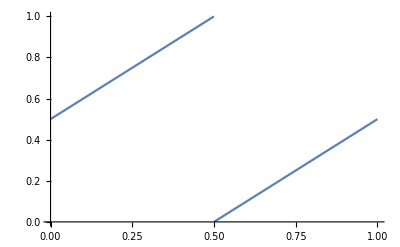

```mathematica
Plot[SawtoothWave[t+1/2],{t,0,1}]
```